# Modelos Matemáticos y Algoritmos - Ejercicio 3

## Jesús Bueno Urbano - 20078941X

## Planteamiento del problema y cálculo de los puntos críticos

```mathematica
V[x_]:=-x^4/4 + (1-λ)*x^3/3 + (λ-1)*x^2/2 + x
Energy[x_,y_]:=y^2/2 + V[x]
```

```mathematica
CriticalV=Solve[V'[x]==0,x];
```

```mathematica
x1=x/.CriticalV[[1]]
x2=x/.CriticalV[[2]]
x3=x/.CriticalV[[3]]
```

1

1/2 (-λ-√(-4+λ^2))

1/2 (-λ+√(-4+λ^2))

```mathematica
FullSimplify[V''[x1]]
FullSimplify[V''[x2]]
FullSimplify[V''[x3]]
```

-2-λ

-1/2 (2+λ) (-2+λ+√(-4+λ^2))

1/2 (2+λ) (2-λ+√(-4+λ^2))

```mathematica
P1:={x1,0};
P2:={x2,0};
P3:={x3,0};
```

## Apartado 2 - Dibujo de las fases

Como hemos visto en el primer apartado del ejercicio, tenemos tres casos 0 < λ < 2, λ = 2 y λ > 2.

### Caso 0 < λ < 2

```mathematica
λ=1;
```

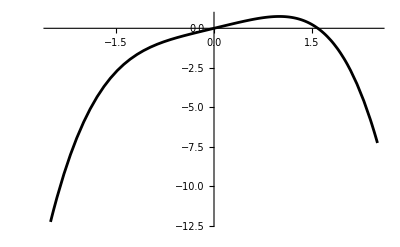

```mathematica
Plot[V[x],{x,-2.5,2.5},PlotStyle->{Black,Thickness[0.005]}]
```

```mathematica
V[x1];
```

```mathematica
f[x_,y_]:=y;
g[x_,y_]:=-V'[x];
```

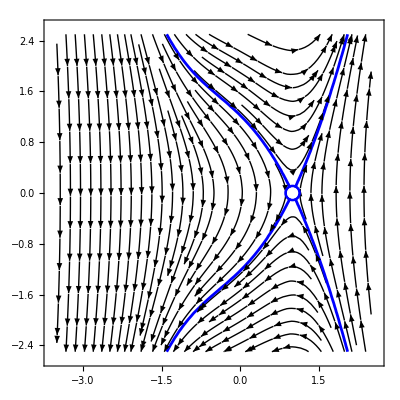

```mathematica
gr11=StreamPlot[{f[x,y],g[x,y]},{x,-3.5,2.5},{y,-2.5,2.5}, StreamStyle-> Black];
gr12=ContourPlot[Energy[x,y]==V[x1], {x, -2.5, 2.5}, {y, -2.5, 2.5}, ContourStyle->{Thickness[0.005],Blue}];
gr13= ListPlot[{P1,P2,P3},PlotStyle->{PointSize[0.03],Blue},PlotRange->All];
gr14=ListPlot[{P1},PlotStyle->{PointSize[0.02],White},PlotRange->All];
gr1=Show[gr11,gr12,gr13,gr14]
```

### Caso λ = 2

```mathematica
λ=2;
```

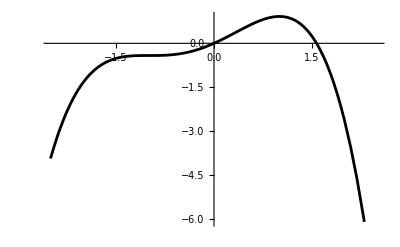

```mathematica
Plot[V[x],{x,-2.5,2.5},PlotStyle->{Black,Thickness[0.005]}]
```

```mathematica
V[x1];
V[x2];
```

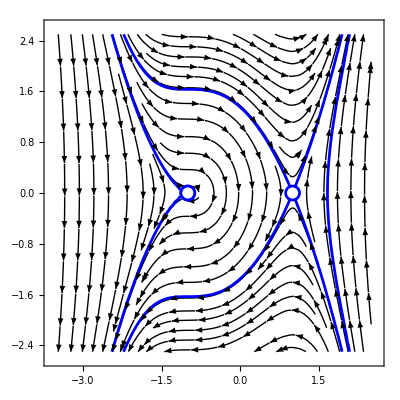

```mathematica
gr21=StreamPlot[{f[x,y],g[x,y]},{x,-3.5,2.5},{y,-2.5,2.5}, StreamStyle-> Black];
gr22=ContourPlot[Energy[x,y]==V[x1], {x, -2.5, 2.5}, {y, -2.5, 2.5}, ContourStyle->{Thickness[0.005],Blue}];
gr23=ContourPlot[Energy[x,y]==V[x2], {x, -2.5, 2.5}, {y, -2.5, 2.5}, ContourStyle->{Thickness[0.005],Blue}];
gr24= ListPlot[{P1,P2,P3},PlotStyle->{PointSize[0.03],Blue},PlotRange->All];
gr25=ListPlot[{P1,P2},PlotStyle->{PointSize[0.02],White},PlotRange->All];
gr2=Show[gr21,gr22,gr23,gr24,gr25]
```

### Caso λ > 2

```mathematica
λ=5/2;
```

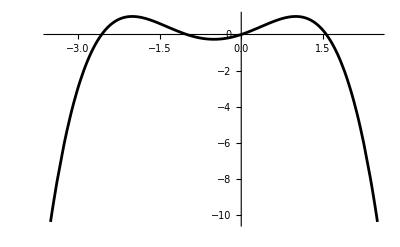

```mathematica
Plot[V[x],{x,-3.5,2.5},PlotStyle->{Black,Thickness[0.005]}]
```

```mathematica
V[x1];
V[x2];
V[x3];
```

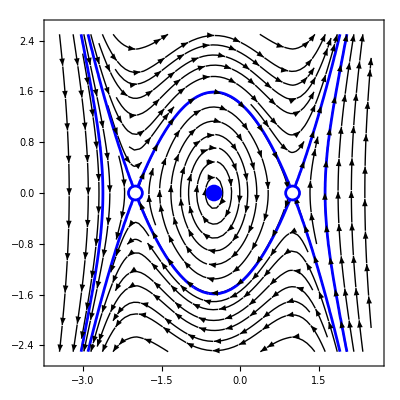

```mathematica
gr31=StreamPlot[{f[x,y],g[x,y]},{x,-3.5,2.5},{y,-2.5,2.5}, StreamStyle-> Black];
gr32=ContourPlot[Energy[x,y]==V[x1], {x, -3.5, 2.5}, {y, -2.5, 2.5}, ContourStyle->{Thickness[0.005],Blue}];
gr33=ContourPlot[Energy[x,y]==V[x3], {x, -3.5, 2.5}, {y, -2.5, 2.5}, ContourStyle->{Thickness[0.005],Blue}];
gr34= ListPlot[{P1,P2,P3},PlotStyle->{PointSize[0.03],Blue},PlotRange->All];
gr35=ListPlot[{P1,P2},PlotStyle->{PointSize[0.02],White},PlotRange->All];
gr3=Show[gr31,gr32,gr33,gr34,gr35]
```

## Apartado 3 - Análisis de la bifurcación

Comenzamos comparando los dibujos de las fases hasta ahora obtenidos.

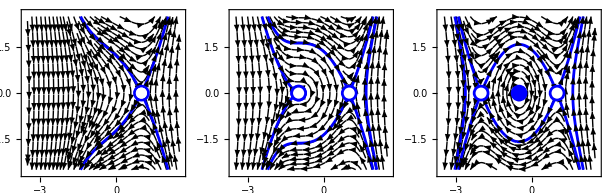

```mathematica
GraphicsGrid[{{gr1,gr2,gr3}}]
```

En el primer gráfico, comenzando por la izquierda, estamos en el caso 0 < λ < 2 y se verifican las condiciones para que V(x) sea un potencial ya que sólo se presenta un punto de silla en el (1,0), siendo éste el único máximo y por tanto no se puede presentar ninguna bifurcación.

En el gráfico central estamos en el caso λ = 2 y como podemos observar hay un punto degenerado, por tanto V(x) no es un potencial genérico y pasamos a analizar la evolución de su comportamiento.

En el gráfico de la derecha estamos en el caso λ > 2, en concreto en el caso λ = 5/2 y como podemos observar en este caso en particular los dos máximos alcanzan el mismo valor, por tanto V(x) no es un potencial genérico y pasamos a analizar la evolución de su comportamiento.

### Evolución alrededor de λ = 2

```mathematica
λ=2.3;
```

```mathematica
graphics0={};
```

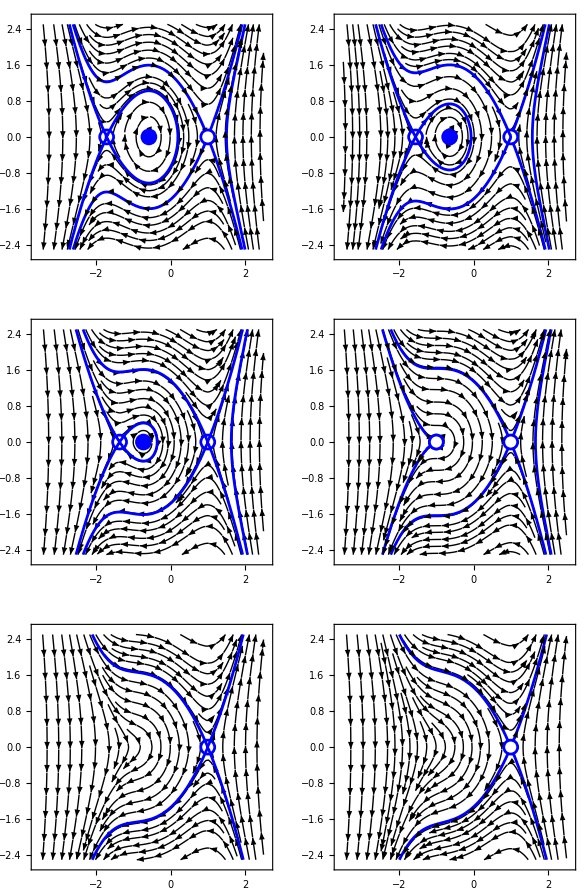

```mathematica
While[λ>1.7,
V[x1];
V[x2];
gr01=StreamPlot[{f[x,y],g[x,y]},{x,-3.5,2.5},{y,-2.5,2.5}, StreamStyle->Black];
gr02=ListPlot[{{x1,0},{x2,0},{x3,0}}, PlotStyle->{PointSize[0.03],Blue}, PlotRange->All];
gr03=ListPlot[{{x1,0},{x2,0}}, PlotStyle->{PointSize[0.02],White}, PlotRange-> All];
gr04=ContourPlot[Energy[x,y]==V[x1], {x,-3.5,2.5},{y,-2.5,2.5}, ContourStyle-> {Thickness[0.005],Blue}];gr05= ContourPlot[Energy[x,y]==V[x2], {x,-3.5,2.5},{y,-2.5,2.5}, ContourStyle-> {Thickness[0.005],Blue}];
gr0=Show[gr01,gr02,gr03,gr04,gr05];
λ=λ-0.1;
graphics0=Join[graphics0,{gr0}]];
graphics={{graphics0[[1]],graphics0[[2]]},{graphics0[[3]],gr2},{graphics0[[5]],graphics0[[6]]}};
GraphicsGrid[graphics]
```

Esta claro que si tomamos λ > 2, y vamos desdenciendiendo el valor hasta alcanzar el valor λ = 2, nos encontramos con una familia de orbitas en la que hay presentes un centro de una homoclina y dos puntos de silla.  Conforme λ disminuye vemos como el centro y un punto de silla se van aproximando hasta que en λ = 2 se rompe y se crea un punto degenerado. Para λ < 2 vemos como el punto degenerado desaparece y nos queda simplemente un punto de silla.

### Evolución alrededor de λ = 5/2

```mathematica
λ=2.8;
```

```mathematica
graphics0={};
```

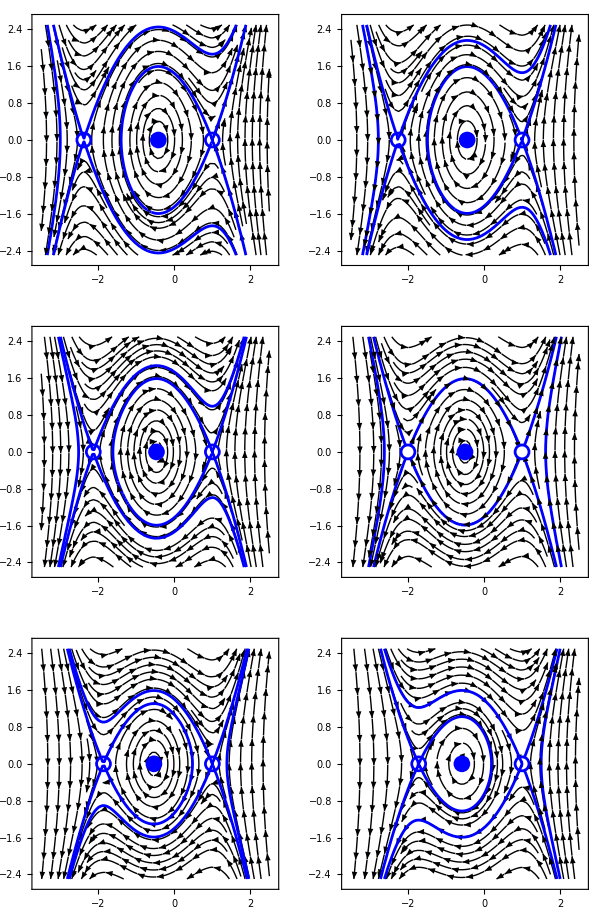

```mathematica
While[λ>2.2,
V[x1];
V[x2];
gr01=StreamPlot[{f[x,y],g[x,y]},{x,-3.5,2.5},{y,-2.5,2.5}, StreamStyle->Black];
gr02=ListPlot[{{x1,0},{x2,0},{x3,0}}, PlotStyle->{PointSize[0.03],Blue}, PlotRange->All];
gr03=ListPlot[{{x1,0},{x2,0}}, PlotStyle->{PointSize[0.02],White}, PlotRange-> All];
gr04=ContourPlot[Energy[x,y]==V[x1], {x,-3.5,2.5},{y,-2.5,2.5}, ContourStyle-> {Thickness[0.005],Blue}];gr05= ContourPlot[Energy[x,y]==V[x2], {x,-3.5,2.5},{y,-2.5,2.5}, ContourStyle-> {Thickness[0.005],Blue}];
gr0=Show[gr01,gr02,gr03,gr04,gr05];
λ=λ-0.1;
graphics0=Join[graphics0,{gr0}]];
graphics={{graphics0[[1]],graphics0[[2]]},{graphics0[[3]],gr3},{graphics0[[5]],graphics0[[6]]}};
GraphicsGrid[graphics]
```

Esta claro que si tomamos λ > 5/2, y vamos desdenciendiendo el valor hasta alcanzar el valor λ = 5/2, nos encontramos con una familia de orbitas en la que hay presentes un centro de una homoclina y dos puntos de silla.Conforme λ disminuye vemos como el centro y un punto de silla se van elejando hasta que en λ = 5/2 se rompe y se crea una órbita heteroclina.Para λ < 2 vemos como el se crea denuevo la situación descrita en el caso anterior.